# Bessel applications (Fraunhofer diffraction)

```mathematica
SetOptions[$FrontEnd, 
 NotebookBrowseDirectory -> "C:\\Users\\thomm\\Documents\\GitHub\\fisica-matematica-2\\extras\\mathematica-notebooks\\bessel"]
```

BesselJ[n,z] gives the Bessel function of the first kind J_n(z). 


BesselY[n,z] gives the Bessel function of the second kind Y_n(z) ... The Neumann function

It satisfies the differential equationz^2 y''+z y'+(z^2-n^2)y=0that we obtained for example in the solution of the Laplace equation in cilindrical coordenates.

       Remenber that:

n=ν is a number (It could be complex number)
       y=y(x) where x is the independent variable

#### Traditional form

```mathematica
BesselJ[n,r]//TraditionalForm
BesselY[n,r]//TraditionalForm
```

nr

nr

#### The single slip (Optics, Eugene Hecht book)

```mathematica
Import["figures/bessel-fig1.png"]
```

Import::nffil: File figures/bessel-fig1.png not found during Import.

$Failed

Intensity of the Fraunhofer diffraction pattern of a circular aperture versus diffraction angle :

```mathematica
Import["figures/bessel-fig3.png"]
```

Import::nffil: File figures/bessel-fig3.png not found during Import.

$Failed

#### Multiple slips

Two slips

```mathematica
Import["figures/bessel-fig4.png"]
```

Import::nffil: File figures/bessel-fig4.png not found during Import.

$Failed

```mathematica
Import["figures/bessel-fig5.png"]
```

Import::nffil: File figures/bessel-fig5.png not found during Import.

$Failed

#### Many slips

```mathematica
Import["figures/bessel-fig6.png"]
```

Import::nffil: File figures/bessel-fig6.png not found during Import.

$Failed

#### Rectangular aperture

```mathematica
Import["figures/bessel-fig7.png"]
```

Import::nffil: File figures/bessel-fig7.png not found during Import.

$Failed

```mathematica
Import["Bessel-fig8.png"]
```

Import::nffil: File Bessel-fig8.png not found during Import.

$Failed

```mathematica
Import["figures/bessel-fig9.png"]
```

Import::nffil: File figures/bessel-fig9.png not found during Import.

$Failed

#### The circular aperture

```mathematica
Import["figures/bessel-fig10.png"]
Import["figures/bessel-fig11.png"]
Import["figures/bessel-fig12.png"]
Import["figures/bessel-fig13.png"]
```

Import::nffil: File figures/bessel-fig10.png not found during Import.

$Failed

Import::nffil: File figures/bessel-fig11.png not found during Import.

$Failed

Import::nffil: File figures/bessel-fig12.png not found during Import.

$Failed

Import::nffil: File figures/bessel-fig13.png not found during Import.

$Failed

#### Plot the function

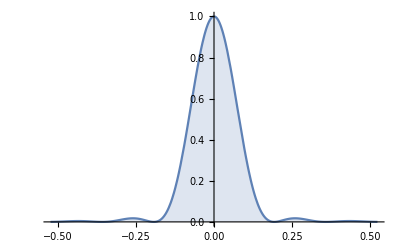

```mathematica
Plot[(2*BesselJ[1,20Sin[θ]]/(20Sin[θ]))^2,{θ,-π/6,π/6},Filling->Axis]
```

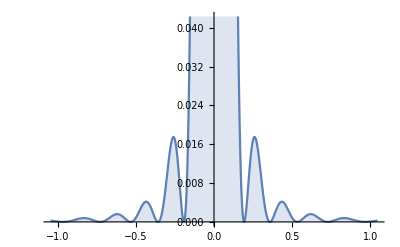

```mathematica
Plot[(2*BesselJ[1,20Sin[θ]]/(20Sin[θ]))^2,{θ,-π/3,π/3},Filling->Axis]
```